```mathematica
SetDirectory["/Users/Apple/Documents"];
```

```mathematica
NDSolve[{Nest[D[#,x]&,a[x,t],4]==-D[D[a[x,t],t],t],NestList[D[#,t]&,a[x,t],1]=={1,-2},NestList[D[#,x]&,a[x,t],3]=={0,0,0,0}},a[x,t],{x,t}]
```

NDSolve::overdet: There are fewer dependent variables, {a[x,t],a^(0,1)[x,t],a^(0,2)[x,t]}, than equations, so the system is overdetermined.

NDSolve[{a^(4,0)[x,t]==-a^(0,2)[x,t],{a[x,t],a^(0,1)[x,t]}=={1,-2},{a[x,t],a^(1,0)[x,t],a^(2,0)[x,t],a^(3,0)[x,t]}=={0,0,0,0}},a[x,t],{x,t}]

```mathematica
DSolve[{x''[t]==-a*x[t],y''[t]==-a*y[t],x[0]==x0,y[0]==y0,x'[0]==w1,y'[0]==w2},{x[t],y[t]},t]
```

{{x[t]→(√a x0 Cos[√a t]+w1 Sin[√a t])/(√a),y[t]→(√a y0 Cos[√a t]+w2 Sin[√a t])/(√a)}}

```mathematica
NestList[D[#,x]&,a[x,t],3]=={0,0,0}
```

False

```mathematica
NestList[D[#,x]&,a[x,t],3]=={0,0,0}/.x->0
```

False

```mathematica
Nest[D[#,x]&,a[x,t],4]
```

a^(4,0)[x,t]

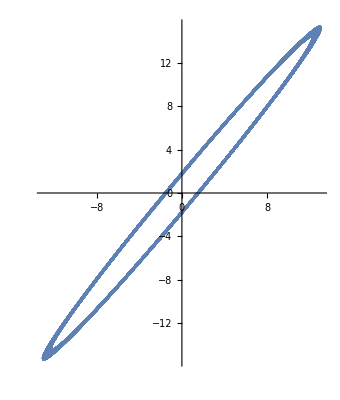

```mathematica
ParametricPlot[Flatten@Evaluate[(Evaluate[{x[t],y[t]}/.%63])/.{a->1,x0->1,y0->3,w1->-13,w2->-15}],{t,0,2000}]
```

```mathematica
Flatten@Evaluate[(Evaluate[{x[t],y[t]}/.%63])/.{a->1,x0->3,y->1,w1->-1,w2->-2}]
```

{3 Cos[t]-Sin[t],y0 Cos[t]-2 Sin[t]}

```mathematica
NDSolve[Evaluate[{α''[t]==-k/(m r0)α[t],β''[t]==-g/l*β[t]+α'[t]^2*β[t]+α'[t]^2/l*r0,α[0]==0,β[0]==5/180*Pi,α'[0]==0.1,β'[0]==0}/.{r0->0.33,k->1,m->1,g->9.8,l->0.3},{α[t],β[t]}],{t,0,10}]
```

{{α[t]→InterpolatingFunction[{{0., 10.}}, <>][t],β[t]→InterpolatingFunction[{{0., 10.}}, <>][t]}}

```mathematica
ParametricPlot[Flatten[Evaluate[{α[t],β[t]}/.%100],{t,0,10}]]
```

```mathematica
Model1[r0_,k_,m_,l_,α0_,β0_,Wα_,Wβ_,EP_]:=Module[{α,β,t,g,data},data=NDSolve[Evaluate[{α''[t]==-k/(m r0)α[t]+2*β'[t]*α'[t],β''[t]==-g/l*Sin[β[t]]+α'[t]^2*β[t]+α'[t]^2/l*r0,α[0]==α0,β[0]==β0,α'[0]==Wα,β'[0]==Wβ}/.{g->9.8},{α[t],β[t]}],{t,0,EP}];
ParametricPlot[Flatten[Evaluate[{r0*α[t],l*β[t]}/.data]],{t,0,EP}]
];
Model2[r0_,m_,l_,a_,α0_,β0_,Wα_,Wβ_,EP_]:=Module[{α,β,t,g,data},data=NDSolve[Evaluate[{α''''[t]==-a*α[t],β''[t]==-g/l*Sin[β[t]]+α'[t]^2*β[t]+α'[t]^2/l*r0,α[0]==α0,β[0]==β0,α'[0]==Wα,β'[0]==Wβ,α''[0]==0,α'''[0]==0}/.{g->9.8},{α[t],β[t]}],{t,0,EP}];
ParametricPlot[Flatten[Evaluate[{r0*α[t],l*β[t]}/.data]],{t,0,EP}]
];
AnimateModel1[r0_,k_,m_,l_,α0_,β0_,Wα_,Wβ_,EP_]:=Module[{α,β,t,g,data},data=NDSolve[Evaluate[{α''[t]==-k/(m r0)α[t]+2*β'[t]*α'[t],β''[t]==-g/l*Sin[β[t]]+α'[t]^2*β[t]+α'[t]^2/l*r0,α[0]==α0,β[0]==β0,α'[0]==Wα,β'[0]==Wβ}/.{g->9.8},{α[t],β[t]}],{t,0,EP}]//Quiet;
Animate[Show[ParametricPlot[Flatten[Evaluate[{(r0+l*Sin[β[t]])*Sin[α[t]],(r0+l*Sin[β[t]])*Cos[α[t]]}/.data]],{t,0,EP},PlotStyle->White,ImageSize->Large],ParametricPlot[Flatten[Evaluate[{(r0+l*Sin[β[t]])*Sin[α[t]],(r0+l*Sin[β[t]])*Cos[α[t]]}/.data]],{t,0,x},PlotStyle->Black]]
,{x,0,EP},RefreshRate->60,AnimationRate->.1]//Quiet
];
```

```mathematica
Export["test.gif",AnimateModel1[0.5,0.1,0.5,0.3,0,5/180*Pi,0.1,0,20]]
```

test.gif

```mathematica
Model2[0.5,0.1,0.5,10,0,5/180*Pi,0.1,0,10]
```

-Graphics-

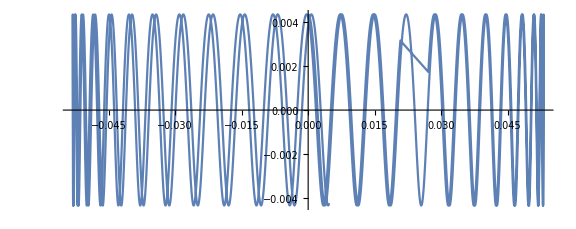

```mathematica
Show[Model1[0.2,0.01,0.5,0.05,0,5/180*Pi,0.1,0,20],ImageSize->Large]
```

```mathematica
Clear[β]
```

```mathematica
Animate[Show[ParametricPlot[{Sin[#1 t],Sin[#2 t]},{t,0,x},PlotRange->{{-1.1,1.1},{-1.1,1.1}}],Graphics[Point[{Sin[#1 x],Sin[#2 x]}]]]&[11,13],{x,-Pi,Pi},RefreshRate->60,AnimationRate->.01]
```

```mathematica
Model1[r0_,k_,m_,l_,μ_,α0_,β0_,Wα_,Wβ_,EP_]:=Module[{α,β,t,g,data},data=NDSolve[Evaluate[{α''[t]==-k/(m r0)α[t]+2*β'[t]*α'[t]-μ,β''[t]==-g/l*Sin[β[t]]+α'[t]^2*β[t]+α'[t]^2/l*r0,α[0]==α0,β[0]==β0,α'[0]==Wα,β'[0]==Wβ}/.{g->9.8},{α[t],β[t]}],{t,0,EP}];
ParametricPlot[Flatten[Evaluate[{r0*α[t],l*β[t]}/.data]],{t,0,EP}]
];
```

```mathematica
Model3[0.2,0.01,0.5,0.05,0,5/180*Pi,0.1,0,20]
```

NDSolve::litarg: To avoid possible ambiguity, the arguments of the dependent variable in {α$10658''[t$10658]==-0.1 α$10658[t$10658]+2 α$10658'[t$10658] β$10658'[t$10658],0.245 (-1+Cos[β$10658[t$10658]])+0.005 α$10658[t$10658]^2+0.000625 (α$10658'[t$10658]^2+β$10658'[t$10658]^2)==0.245 (-1+Cos[β$10658[0]])+0.005 α$10658[0]^2+0.000625 (α$10658'[0]^2+β$10658'[0]^2)} should literally match the independent variables.

ReplaceAll::reps: {NDSolve[{α$10658''[0.000408163]==-0.1 α$10658[0.000408163]+2 α$10658'[0.000408163] β$10658'[0.000408163],0.245 (-1+Cos[«1»])+0.005 α$10658[«1»]^2+0.000625 (Power[«2»]+Power[«2»])==0.245 (-1+Cos[«1»])+0.005 («1»)^2+0.000625 (Power[«2»]+Power[«2»]),«7»'[0]==0.1,β$10658'[0]==0},«1»,{«1»}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000408163 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{α$10658''[0.000408163]==-0.1 α$10658[0.000408163]+2 α$10658'[0.000408163] β$10658'[0.000408163],0.245 (-1+Cos[«1»])+0.005 α$10658[«1»]^2+0.000625 (Power[«2»]+Power[«2»])==0.245 (-1+Cos[«1»])+0.005 («1»)^2+0.000625 (Power[«2»]+Power[«2»]),«7»'[0]==0.1,β$10658'[0]==0},«1»,{«1»}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
Mean[{1.27,1.31,1.29}]
```

1.29

```mathematica
Mean[{2.39,2.62,2.09}]
```

2.36667

```mathematica
SetDirectory["/Users/Apple/Documents"];
```

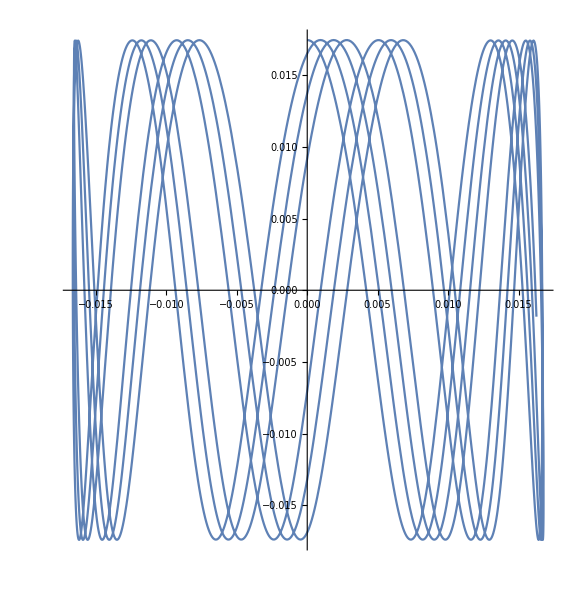

```mathematica
Show[Model1[0.2,0.1,0.5,0.2,0,5/180*Pi,0.1,0,20],ImageSize->Large]
```

```mathematica
Export["fig1.eps",%24]
```

fig1.eps

```mathematica
TeXForm["Show[Model1[0.2,0.1,0.5,0.2,0,5/180*Pi,0.1,0,20],ImageSize→Large]"]
```

\text{Show[Model1[0.2,0.1,0.5,0.2,0,5/180*Pi,0.1,0,20],ImageSize$\to $Large]}